```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPA_Tscaling_mub0_v2/buffer/mSigma.dat"]];
T0=Flatten[Import["./LPA_Tscaling_mub0_v2/buffer/TMeV.dat"]];
t=-(T0-T0[[1]](*+0.00015*))/(T0[[1]](*-0.00015*));
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub700/buffer/mSigma.dat"]];
T700=Flatten[Import["./LPA_Tscaling_mub700/buffer/TMeV.dat"]];
t=-(T700-T700[[1]])/T700[[1]];
datamub700=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub700=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T700]-2}]]}];
b1mub700linear=Transpose[{T700[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T700]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub705/buffer/mSigma.dat"]];
T705=Flatten[Import["./LPA_Tscaling_mub705/buffer/TMeV.dat"]];
t=-(T705-T705[[1]])/T705[[1]];
datamub705=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub705=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub705[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T705]-2}]]}];
b1mub705linear=Transpose[{T705[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub705[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T705]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_mub706/buffer/mSigma.dat"]];
T706=Flatten[Import["./LPA_Tscaling_mub706/buffer/TMeV.dat"]];
t=-(T706-T706[[1]])/T706[[1]];
datamub706=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub706=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub706[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T706]-2}]]}];
b1mub706linear=Transpose[{T706[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub706[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T706]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_mub706p3/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub706p3/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub706p3=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1mub706p3linear=Transpose[{T[[2;;Length[t]-2]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_TCP/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_TCP/buffer/TMeV.dat"]];
deltaT=0.00;
t=-(T-T[[1]]+deltaT)/(T[[1]]-deltaT);
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1TCP=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1TCPlinear=Transpose[{T[[2;;Length[t]-2]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
```

## Plot

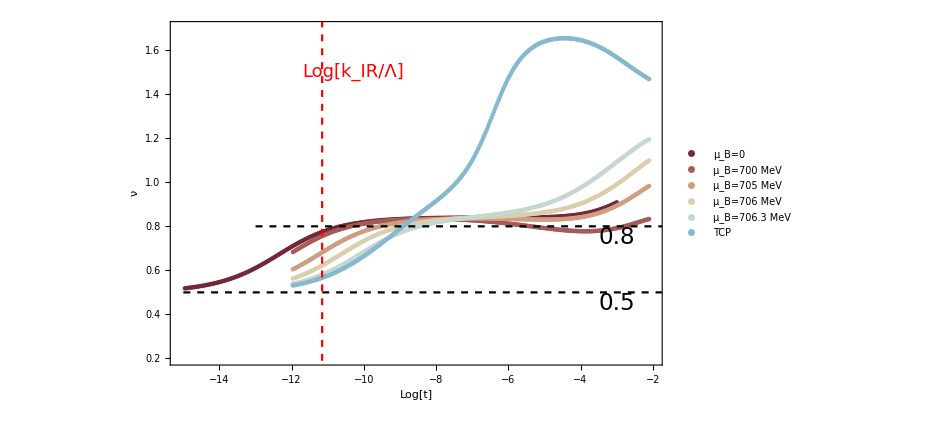

```mathematica
plotT=Show[ListPlot[{b1mub0,b1mub700,b1mub705,b1mub706,b1mub706p3,b1TCP},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.15}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=700 MeV","μ_B=705 MeV","μ_B=706 MeV","μ_B=706.3 MeV","TCP"},LabelStyle->16],{0.17,0.7}],
PlotRange->{{-15.1,-2},{0.2,1.7}},AxesOrigin->{-15.1,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.8},{10,0.8}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-15,0.5},{10,0.5}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-11.1563,0.},{-11.1563,10}},PlotStyle->{Red,Dashed}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.75}],Text[Style["0.5",23],{-3,0.45}],Text[Style["Log[k_IR/Λ]",18,Red],{-10.3,1.5}]}]
```

```mathematica
Export["./nu_v1.pdf",plotT]
```

./nu_v1.pdf